```mathematica
$Version
Clear["Global`*"]
```

14.0.0 for Microsoft Windows (64-bit) (December 13, 2023)

```mathematica
LatticeEndIndex = 100;
```

```mathematica
J[0,α_]=1;
J[n_,α_]:=J[n,α]=1/Abs[n]^(1+α);
```

```mathematica
wB = 1/2;
```

```mathematica
wA = 2 wB;
```

```mathematica
q[0,ϵ_,α_,wA_]:=Sqrt[wA+2 ϵ  J[0,α]];
q[n_Integer?Positive,ϵ_,α_,wA_]:=q[n,ϵ,α,wA]=ϵ  (J[n,α]*q[0,ϵ,α,wA]+Sum[(J[n-m,α]+J[n+m,α])*q[m,ϵ,α,wA],{m,1,n-1}])/(ϵ  (2*J[0,α]-J[2*n,α])+wA)//Simplify
```

```mathematica
onsiteSequence=q[#,1,1,1]&/@Range[0,LatticeEndIndex ];
```

```mathematica
g[0,ϵ_,α_,wB_]:=Sqrt[wB+ϵ(2J[0,α]-J[1,α])]
g[1,ϵ_,α_,wB_]:=Sqrt[wB+ϵ(2J[0,α]-J[1,α])]
g[n_Integer?Positive,ϵ_,α_,wB_]:=g[n,ϵ,α,wB]= ϵ Sum[(J[n-m,α]+J[n+m-1,α])*g[m,ϵ,α,wB],{m,1,n-1}]/(ϵ  (2*J[0,α]-J[2*n-1,α])+wB)//Simplify
```

```mathematica
offsiteSequence=g[#,1,1,1]&/@Range[0,LatticeEndIndex ];
```

```mathematica
EA[ϵ_,α_]:=ϵ Sum[Abs[  Part[onsiteSequence,n] - Part[onsiteSequence,1] ]^2/n^(1+α) + 1/2 Sum[If[m!=n,1/Abs[n-m]^(1+α)+1/Abs[n+m]^(1+α),0]*Abs[Part[onsiteSequence,n]-Part[onsiteSequence,m]]^2,{m,2,LatticeEndIndex}],{n,2,LatticeEndIndex }]-(1/4 Part[onsiteSequence,1]^4+1/2 Sum[Part[onsiteSequence,n]^4,{n,2,LatticeEndIndex }])
```

```mathematica
EB[ϵ_,α_]:= ϵ Sum[(1/n^(1+α)+1/(n-1)^(1+α))Abs[Part[offsiteSequence,n] - Part[offsiteSequence,1]]^2+1/2 Sum[If[m!=n,1/Abs[n-m]^(1+α)+1/Abs[n+m-1]^(1+α),0]*Abs[Part[offsiteSequence,n]-Part[offsiteSequence,m]]^2,{m,3,LatticeEndIndex}],{n,3,LatticeEndIndex}]-1/2 Sum[Part[offsiteSequence,n]^4,{n,2,LatticeEndIndex}]
```

```mathematica
EB[0,1]//N
```

-2.08636

```mathematica
Part[onsiteSequence,2]//N
```

0.629837

```mathematica
Part[onsiteSequence,1]/(1+(2-J[2,1]))//N
```

0.629837

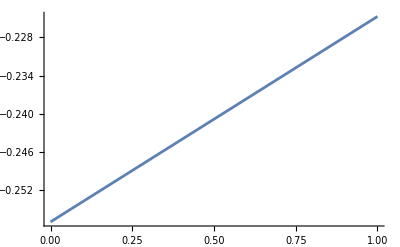

```mathematica
Plot[EA[ϵ,1]-EB[ϵ,1],{ϵ,0,1}]
```

Corollary 5.3 values for EA and EB below.

```mathematica
EACorollary[ϵ_,wA_,α_]:= -wA^2/4-ϵ^2(2Zeta[2+2α]+Zeta[1+α]^2);
```

```mathematica
EBCorollary[ϵ_,wB_,α_]:=
```